```mathematica
_________________________________==========++++++++++++++++++++++++++++++++++++++=========+________
```

```mathematica
Полученные ур-я движения для секступольного возмущения из ноутбука eqA,eqB;
```

```mathematica
Jastr=(h1 a^2Sin[3ϕa]+a b (Cos[2 ϕa+ϕb]h111+h112 Sin[2ϕa+ϕb])+b^2(Cos[ϕa+2ϕb]h121+h122 Sin[ϕa+2ϕb])) 2a/.{a->Sqrt[Ja],b->Sqrt[Jb]};
Jbstr=(h2 b^2Sin[3ϕb]+a^2 (Cos[2ϕa+ϕb]h211+h212 Sin[2ϕa+ϕb])+a b(Cos[ϕa+2ϕb]h221+h222 Sin[ϕa+2ϕb]))2b/.{a->Sqrt[Ja],b->Sqrt[Jb]};
ϕastr=(h1 a Cos[3ϕa]+ b (Cos[2 ϕa+ϕb]h112-h111 Sin[2ϕa+ϕb])+b^2(-Sin[ϕa+2ϕb]h121+h122 Cos[ϕa+2ϕb])/a+na+1/3+Δ+δ)/.{a->Sqrt[Ja],b->Sqrt[Jb]};
ϕbstr=(h2 b Cos[3ϕb]+a ^2(Cos[2ϕa+ϕb]h212-h211 Sin[2ϕa+ϕb])/b+a(Cos[ϕa+2ϕb]h222-h221 Sin[ϕa+2ϕb])+nb+1/3+Δ-δ)/.{a->Sqrt[Ja],b->Sqrt[Jb]};
```

```mathematica
_______для дифуров;
```

```mathematica
Jastrd=Jastr/.{Ja->Ja[t],Jb->Jb[t],ϕa->ϕa[t],ϕb->ϕb[t]};
Jbstrd=Jbstr/.{Ja->Ja[t],Jb->Jb[t],ϕa->ϕa[t],ϕb->ϕb[t]};
ϕastrd=ϕastr/.{Ja->Ja[t],Jb->Jb[t],ϕa->ϕa[t],ϕb->ϕb[t]};
ϕbstrd=ϕbstr/.{Ja->Ja[t],Jb->Jb[t],ϕa->ϕa[t],ϕb->ϕb[t]};
```

```mathematica
_______получение гамильтониана;
```

```mathematica
Simplify[Integrate[Jastr,ϕa]]
```

-2/3 h1 Ja^(3/2) Cos[3 ϕa]-h112 Ja √Jb Cos[2 ϕa+ϕb]-2 h122 √Ja Jb Cos[ϕa+2 ϕb]+h111 Ja √Jb Sin[2 ϕa+ϕb]+2 h121 √Ja Jb Sin[ϕa+2 ϕb]

```mathematica
Simplify[Integrate[ϕastr,Ja]]
```

Ja/3+Ja na+Ja δ+Ja Δ+2/3 h1 Ja^(3/2) Cos[3 ϕa]+Ja √Jb (h112 Cos[2 ϕa+ϕb]-h111 Sin[2 ϕa+ϕb])+2 √Ja Jb (h122 Cos[ϕa+2 ϕb]-h121 Sin[ϕa+2 ϕb])

```mathematica
Simplify[Integrate[ϕbstr,Jb]]
```

Jb/3+Jb nb-Jb δ+Jb Δ+2/3 h2 Jb^(3/2) Cos[3 ϕb]+2 Ja √Jb (h212 Cos[2 ϕa+ϕb]-h211 Sin[2 ϕa+ϕb])+√Ja Jb (h222 Cos[ϕa+2 ϕb]-h221 Sin[ϕa+2 ϕb])

```mathematica
H=Simplify[Ja/3+Ja na+Ja δ+Ja Δ+Jb/3+Jb nb-Jb δ+Jb Δ+2/3 h1 Ja^(3/2) Cos[3 ϕa]+2/3 h2 Jb^(3/2) Cos[3 ϕb]+Ja √Jb (h112 Cos[2 ϕa+ϕb]-h111 Sin[2 ϕa+ϕb])+2 √Ja Jb (h122 Cos[ϕa+2 ϕb]-h121 Sin[ϕa+2 ϕb])]
```

1/3 (Ja+Jb+3 Ja na+3 Jb nb+3 Ja δ-3 Jb δ+3 Ja Δ+3 Jb Δ+2 h1 Ja^(3/2) Cos[3 ϕa]+2 h2 Jb^(3/2) Cos[3 ϕb]+3 Ja √Jb (h112 Cos[2 ϕa+ϕb]-h111 Sin[2 ϕa+ϕb])+6 √Ja Jb (h122 Cos[ϕa+2 ϕb]-h121 Sin[ϕa+2 ϕb]))

```mathematica
HH=Simplify[Ja/3+Ja na+Ja δ+Ja Δ+Jb/3+Jb nb-Jb δ+Jb Δ+2/3 h1 Ja^(3/2) Cos[3 ϕa]+2/3 h2 Jb^(3/2) Cos[3 ϕb]+Ja √Jb (h11 Cos[2 ϕa+ϕb+δ1])+2 √Ja Jb (h12 Cos[ϕa+2 ϕb+δ2])];
```

```mathematica
(*правильный гамильтониан для δ1, δ2=0; ϕa=ϕa+Ψa,ϕb=ϕb+Ψb:*)
h=2/3 h1 Jx^(3/2) Cos[3 (ϕx+(1/3+Δ+η/2) s/R)]+2/3 h2 Jy^(3/2) Cos[3 (ϕy+(1/3+Δ-η/2) s/R)]+Jx √Jy (h11 Cos[2 ϕx+ϕy+δ1+(2(1/3+Δ+η/2)+(1/3+Δ-η/2))s/R])+√Jx Jy (h12 Cos[ϕx+2 ϕy+δ2+((1/3+Δ+η/2)+2(1/3+Δ-η/2))s/R]);
```

```mathematica
(*дальше старые не очень полезные записи*)
```

```mathematica
Simplify[D[HH,ϕa]]
```

-2 √Ja (h1 Ja Sin[3 ϕa]+h11 √Ja √Jb Sin[δ1+2 ϕa+ϕb]+h12 Jb Sin[δ2+ϕa+2 ϕb])

```mathematica
Simplify[D[HH,ϕb]]
```

-√Jb (2 h2 Jb Sin[3 ϕb]+h11 Ja Sin[δ1+2 ϕa+ϕb]+4 h12 √Ja √Jb Sin[δ2+ϕa+2 ϕb])

```mathematica
Simplify[D[H,ϕa]]
```

-2 √Ja (h111 √Ja √Jb Cos[2 ϕa+ϕb]+h121 Jb Cos[ϕa+2 ϕb]+h1 Ja Sin[3 ϕa]+h112 √Ja √Jb Sin[2 ϕa+ϕb]+h122 Jb Sin[ϕa+2 ϕb])

```mathematica
Simplify[D[H,ϕb]]
```

-2 h2 Jb^(3/2) Sin[3 ϕb]-Ja √Jb (h111 Cos[2 ϕa+ϕb]+h112 Sin[2 ϕa+ϕb])-4 √Ja Jb (h121 Cos[ϕa+2 ϕb]+h122 Sin[ϕa+2 ϕb])

```mathematica
Expand[Simplify[h2 Jb^3/2 (-2 √Ja (h111 √Ja √Jb Cos[2 ϕa+ϕb]+h121 Jb Cos[ϕa+2 ϕb]+h1 Ja Sin[3 ϕa]+h112 √Ja √Jb Sin[2 ϕa+ϕb]+h122 Jb Sin[ϕa+2 ϕb]))+h1 Ja^3/2 (-2 h2 Jb^(3/2) Sin[3 ϕb]-Ja √Jb (h111 Cos[2 ϕa+ϕb]+h112 Sin[2 ϕa+ϕb])-4 √Ja Jb (h121 Cos[ϕa+2 ϕb]+h122 Sin[ϕa+2 ϕb]))]]
```

-1/2 h1 h111 Ja^4 √Jb Cos[2 ϕa+ϕb]-h111 h2 Ja Jb^(7/2) Cos[2 ϕa+ϕb]-2 h1 h121 Ja^(7/2) Jb Cos[ϕa+2 ϕb]-h121 h2 √Ja Jb^4 Cos[ϕa+2 ϕb]-h1 h2 Ja^(3/2) Jb^3 Sin[3 ϕa]-h1 h2 Ja^3 Jb^(3/2) Sin[3 ϕb]-1/2 h1 h112 Ja^4 √Jb Sin[2 ϕa+ϕb]-h112 h2 Ja Jb^(7/2) Sin[2 ϕa+ϕb]-2 h1 h122 Ja^(7/2) Jb Sin[ϕa+2 ϕb]-h122 h2 √Ja Jb^4 Sin[ϕa+2 ϕb]

```mathematica
Jsumstr=(Cos[2 ϕa+ϕb](-1/2 h1 h111 Ja^4 √Jb -h111 h2 Ja Jb^(7/2))+ Sin[2 ϕa+ϕb](-1/2 h1 h112 Ja^4 √Jb-h112 h2 Ja Jb^(7/2) ))+(Cos[ϕa+2 ϕb](-2 h1 h121 Ja^(7/2)-h121 h2 √Ja Jb^4)+ Sin[ϕa+2 ϕb](-2 h1 h122 Ja^(7/2) Jb-h122 h2 √Ja Jb^4))
```

```mathematica
FullSimplify[TrigExpand[H]]
```

1/3 (Ja+Jb+3 Ja na+3 Jb nb+3 Ja δ-3 Jb δ+3 (Ja+Jb) Δ+2 h1 Ja^(3/2) Cos[3 ϕa]+√Jb (2 h2 Jb Cos[3 ϕb]+3 h112 Ja Cos[2 ϕa+ϕb]+6 h122 √Ja √Jb Cos[ϕa+2 ϕb]-3 h111 Ja Sin[2 ϕa+ϕb])-6 h121 √Ja Jb Sin[ϕa+2 ϕb])

```mathematica
Simplify[(Ja/3+Ja na+Ja δ+Ja Δ+Jb/3+Jb nb-Jb δ+Jb Δ)/.{Ja->1/4 (x^2+(2px-x)^2),Jb->1/4 (y^2+(2py-y)^2)}]
```

1/6 (x^2+3 na x^2+y^2+3 nb y^2+3 x^2 δ-3 y^2 δ+3 x^2 Δ+3 y^2 Δ-2 py y (1+3 nb-3 δ+3 Δ)-2 px x (1+3 na+3 δ+3 Δ)+py^2 (2+6 nb-6 δ+6 Δ)+px^2 (2+6 na+6 δ+6 Δ))

```mathematica
H1=2/3 h1 x^3+h112 x^2 y+2 h122 x y^2+2/3 h2 y^3-2 h111 √Ja x y Sin[ϕa]-2 h121 √Ja y^2Sin[ϕa]-2 h1 Ja x Sin[ϕa]^2-h112 Ja y Sin[ϕa]^2-h111 √Jb x^2 Sin[ϕb]-4 h121 √Jb x y Sin[ϕb]-2 h112  √(Jb Ja)  Sin[ϕa] Sin[ϕb]-4 h122 √(Jb Ja)y Sin[ϕa] Sin[ϕb]+h111 Ja √Jb Sin[ϕa]^2 Sin[ϕb]-2 h122  Jb x Sin[ϕb]^2-2 h2 Jb y Sin[ϕb]^2+2 h121 √Ja Jb Sin[ϕa] Sin[ϕb]^2;
```

```mathematica
HH=FullSimplify[(H1/.{√Ja->(x-px)/Sin[ϕa],√Jb->(y-py)/Sin[ϕb],Ja->((x-px)/Sin[ϕa])^2,Jb->((y-py)/Sin[ϕb])^2,√(Jb Ja)->((x-px)/Sin[ϕa])((y-py)/Sin[ϕb])})+1/6 (x^2+3 na x^2+y^2+3 nb y^2+3 x^2 δ-3 y^2 δ+3 x^2 Δ+3 y^2 Δ-2 py y (1+3 nb-3 δ+3 Δ)-2 px x (1+3 na+3 δ+3 Δ)+py^2 (2+6 nb-6 δ+6 Δ)+px^2 (2+6 na+6 δ+6 Δ))]
```

1/6 (-8 h1 x^3-12 x y (h112+2 (h121+h122) y)+2 py (6 h112 x+y (-1-3 nb+24 h122 x+12 h2 y+3 δ-3 Δ))+6 px^2 (1/3+na-2 h1 x-h112 y+h111 (-py+y)+δ+Δ)+y^2 (1+3 nb-8 h2 y-3 δ+3 Δ)+2 py^2 (1+3 nb+6 h121 x-6 h122 x-6 h2 y-3 δ+3 Δ)+x^2 (1+3 na-12 h111 y+3 δ+3 Δ)-2 px (6 h112 py+x+3 na x-6 h111 py x+6 h121 py (py-2 y)-6 h112 (1+x) y+12 h122 (py-y) y+3 x (-4 h1 x+δ+Δ)))

```mathematica
xstr=Simplify[D[HH,px]]
ystr=Simplify[D[HH,py]];
pxstr=-Simplify[D[HH,x]];
pystr=-Simplify[D[HH,y]];
```

1/6 (12 px (1/3+na-2 h1 x-h112 y+h111 (-py+y)+δ+Δ)-2 (6 h112 py+x+3 na x-6 h111 py x+6 h121 py (py-2 y)-6 h112 (1+x) y+12 h122 (py-y) y+3 x (-4 h1 x+δ+Δ)))

```mathematica
solxy =Flatten[NSolve[{xstr== 0 ,ystr==0,pxstr==0,pystr==0}/.{h1->-1,h2->-1,h111->1,h112->1,h121->1,h122->1,h211->1,h212->1,h221->2,h222->2,na->2,nb->4,Δ->0} ,{x,y,px,py}]]
```

{x→0,y→0,px→0,py→0,56,x→1,y→Root[8.11859×10^22+36+22 1&,15],px→(2.2063×10^242 Root[1&,15]+1+1836)/(130+1.18947×10^193 δ^88),py→(5.98577×10^241 Root[8.11859×10^22+2.24434×10^23 δ+35+6.33705×10^27 #1^15&,15]+1825)/(9.85619×10^240+4.91502×10^241 δ+1.76614×10^242 δ^2+7.08142×10^242 δ^3+129)}
 |  |  |  |

```mathematica
solxy[[109]];
```

$Aborted

```mathematica
x/.solxy[[5]]
```

1/(6.89933×10^241+3.7362×10^242 δ+1.38375×10^243 δ^2+5.48684×10^243 δ^3+131)
 |  |  |  |

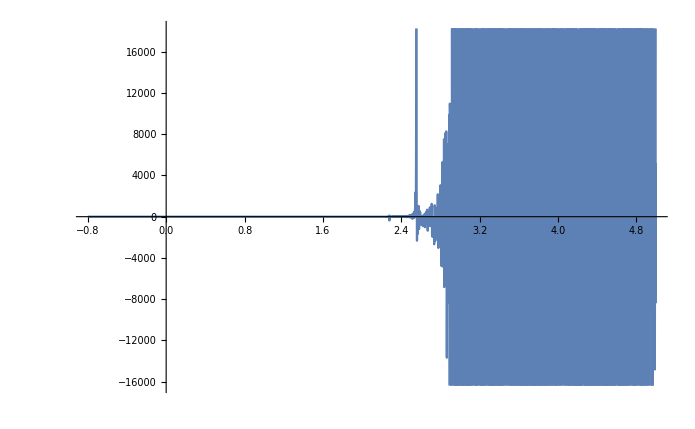

```mathematica
Plot[{{{1/(6.899332932170262*^241+3.736199173872022*^242 δ+1.3837501929114227*^243 δ^2+5.486838176040627*^243 δ^3+131)}, {{{, , , , }}}}},{δ,-0.8,5}]
```

```mathematica
Manipulate[ContourPlot[HH/.{h1->-1,h2->-1,h111->0,h112->2,h121->0,h122->1,h211->0,h212->1,h221->0,h222->2,x->1.8739980602645248,px->4.814271754701366,na->2,nb->4,δ->a1,Δ->0},{y,-1,6},{py,-1,3}],{a1,-0.5,0.5}]
```

```mathematica
Manipulate[ContourPlot[H/.{h1->1,h2->1,h111->1,h112->1,h121->1,h122->1,h211->1,h212->1,h221->1,h222->1,ϕa->0,Ja->1,na->2,nb->4,δ->a1,Δ->0},{ϕb,0,π},{Jb,0,1}],{a1,-0.5,0.5}]
```

```mathematica
проверка на гамильтоновость;
```

```mathematica
Simplify[D[Jastr,Ja]]
```

2 h111 √Jb Cos[2 ϕa+ϕb]+(h121 Jb Cos[ϕa+2 ϕb]+3 h1 Ja Sin[3 ϕa]+2 h112 √Ja √Jb Sin[2 ϕa+ϕb]+h122 Jb Sin[ϕa+2 ϕb])/(√Ja)

```mathematica
Simplify[D[ϕastr,ϕa]]
```

-3 h1 √Ja Sin[3 ϕa]-2 √Jb (h111 Cos[2 ϕa+ϕb]+h112 Sin[2 ϕa+ϕb])-(Jb (h121 Cos[ϕa+2 ϕb]+h122 Sin[ϕa+2 ϕb]))/(√Ja)

```mathematica
соотношения, следующие из eqA, eqB; h:1й индекс - отнош. к A/B, 2й-1для (2ϕa+ϕb),2для(ϕa+2ϕb),3й-1Re,2Im;
```

```mathematica
(* h111 = 2 h211, h112 = 2 h212, 2 h121 = h221, 2 h122 = h222 *) (это в общем виде)
(*для свободной от sqew quad системы: h122->1/4 wx wy^2, h121->0, h111->0, h112->0,h1->-1/4wx^3, h2->0*)
```

```mathematica
дифур->траектории движения;
```

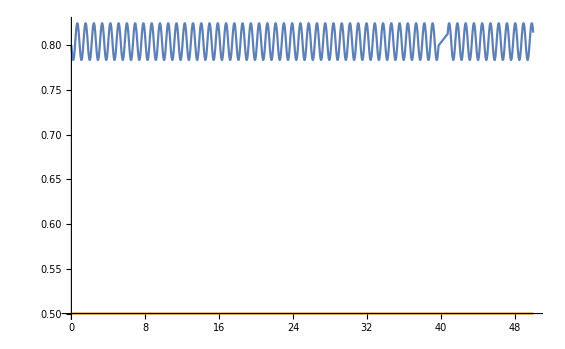

```mathematica
s=NDSolve[{Ja'[t]==Jastrd,Jb'[t]==Jbstrd,ϕa'[t]==ϕastrd,ϕb'[t]==ϕbstrd,Ja[0]==0.8,Jb[0]==0.5,ϕa[0]==10,ϕb[0]==0}/.{h1->0.1,h2->0,h111->0,h112->0,h121->0,h122->0,h211->0,h212->0,h221->0,h222->0,na->2,nb->4,Δ->0,δ->0.01},{Ja[t],ϕa[t],Jb[t],ϕb[t]},{t,0,50}];
Plot[Evaluate[{Ja[t],Jb[t]}/.s,{t,0,50}]]
```

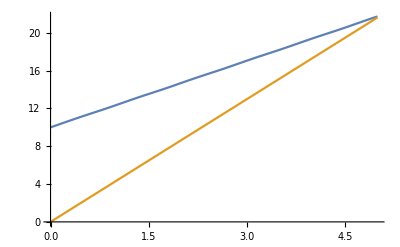

```mathematica
Plot[Evaluate[{ϕa[t],ϕb[t]}/.s,{t,0,5}]]
```

```mathematica
(((ϕa[t]/.s)/.{t->50})-(((ϕa[t]/.s)/.{t->0})))/50
(((ϕb[t]/.s)/.{t->50})-(((ϕb[t]/.s)/.{t->0})))/50
```

{2.34107}

{4.32333}

```mathematica
при таких параметрах (и всех других какие пробовал)-расходимость;
```

```mathematica
поиск стационарных точек;
```

```mathematica
{Jastr== 0 ,Jbstr==0,ϕbstr==0,ϕastr==0}/.{h1->-1,h2->-1,h111->0,h112->0,h121->0,h122->1,h211->0,h212->0,h221->0,h222->2,na->2,nb->4,Δ->0,δ->0.01}
```

{2 √Ja (-Ja Sin[3 ϕa]+Jb Sin[ϕa+2 ϕb])==0,2 √Jb (-Jb Sin[3 ϕb]+2 √Ja √Jb Sin[ϕa+2 ϕb])==0,4.32333-√Jb Cos[3 ϕb]+2 √Ja Cos[ϕa+2 ϕb]==0,2.34333-√Ja Cos[3 ϕa]+(Jb Cos[ϕa+2 ϕb])/(√Ja)==0}

```mathematica
sol =Flatten[NSolve[{Jastr== 0 ,Jbstr==0,ϕbstr==0,ϕastr==0}/.{h1->-1,h2->-1,h111->0,h112->0,h121->0,h122->1,h211->0,h212->0,h221->0,h222->2,na->2,nb->4,Δ->0,δ->0.01} ,{a,b,ϕa,ϕb}]]
```

$Aborted

```mathematica
sol[[96]];
```

```mathematica
ϕb/.{sol[[4]],Δ->0.5}
ϕb/.{sol[[8]],Δ->0.5}
ϕb/.{sol[[12]],Δ->0.5}
ϕb/.{sol[[16]],Δ->0.5}
```

ConditionalExpression[1. (3.14159+6.28319 C[2]),C[2]∈ℤ]

ConditionalExpression[6.28319 C[2],C[2]∈ℤ]

ConditionalExpression[1. (3.14159+6.28319 C[2]),C[2]∈ℤ]

ConditionalExpression[6.28319 C[2],C[2]∈ℤ]

```mathematica
(a/.{sol[[1]]})/.{Δ->a1,n->2}
```

0.333333 (-7.-3. a1+3. δ)

```mathematica
Manipulate[Plot[{(a/.{sol[[1]]})/.{Δ->a1,n->0},(a/.{sol[[5]]})/.{Δ->a1,n->0},(a/.{sol[[9]]})/.{Δ->a1,n->0},(a/.{sol[[13]]})/.{Δ->a1,n->0}},{δ,0,0.5}],{a1,-5,5}]
```

Part::partw: Part 1 of {} does not exist.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 5 of {} does not exist.

ReplaceAll::reps: {{}⟦5⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 9 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

ReplaceAll::reps: {{}⟦9⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

```mathematica
Manipulate[Plot[{(b/.{sol[[2]]})/.{Δ->a1,n->0},(b/.{sol[[6]]})/.{Δ->a1,n->0},(b/.{sol[[10]]})/.{Δ->a1,n->0},(b/.{sol[[14]]})/.{Δ->a1,n->0}},{δ,0,0.5}],{a1,-5,5}]
```

Part::partw: Part 10 of {a→0.166667 (-1.41417-4.24264 n-4.24264 Δ),b→0.0833333 (-1.41426-4.24264 n-4.24264 Δ),ϕb→ConditionalExpression[-2. ϕa+1. (-0.785398+6.28319 C[«1»]),C[1]∈],a→0.166667 («19»+«1»+«18» Δ),b→0.0833333 (1.41426+4.24264 n+4.24264 Δ),ϕb→ConditionalExpression[-2. ϕa+1. (2.35619+6.28319 C[«1»]),C[1]∈]} does not exist.

ReplaceAll::reps: {{a→0.166667 (-1.41417-4.24264 n-4.24264 Δ),b→0.0833333 (-1.41426-4.24264 n-4.24264 Δ),ϕb→ConditionalExpression[-2. ϕa+1. Plus[«2»],C[1]∈],a→0.166667 (1.41417+4.24264 n+4.24264 Δ),b→0.0833333 (1.41426+4.24264 n+4.24264 Δ),ϕb→ConditionalExpression[-2. ϕa+1. Plus[«2»],C[1]∈]}⟦10⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 10 of {a→3.29984,b→1.64991,ϕb→ConditionalExpression[-2. ϕa+1. (-0.785398+6.28319 C[«1»]),C[1]∈],a→-3.29984,b→-1.64991,ϕb→ConditionalExpression[-2. ϕa+1. (2.35619+6.28319 C[«1»]),C[1]∈]} does not exist.

ReplaceAll::reps: {{a→3.29984,b→1.64991,ϕb→ConditionalExpression[-2. ϕa+1. Plus[«2»],C[1]∈],a→-3.29984,b→-1.64991,ϕb→ConditionalExpression[-2. ϕa+1. Plus[«2»],C[1]∈]}⟦10⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 10 of {a→0.166667 (-1.37088-4.24264 n-4.24264 Δ),b→0.0833333 (-1.45755-4.24264 n-4.24264 Δ),ϕb→ConditionalExpression[-2. ϕa+1. (-0.785398+6.28319 C[«1»]),C[1]∈],a→0.166667 («19»+«1»+«18» Δ),b→0.0833333 (1.45755+4.24264 n+4.24264 Δ),ϕb→ConditionalExpression[-2. ϕa+1. (2.35619+6.28319 C[«1»]),C[1]∈]} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

ReplaceAll::reps: {{a→0.166667 (-1.37088-4.24264 n-4.24264 Δ),b→0.0833333 (-1.45755-4.24264 n-4.24264 Δ),ϕb→ConditionalExpression[-2. ϕa+1. Plus[«2»],C[1]∈],a→0.166667 (1.37088+4.24264 n+4.24264 Δ),b→0.0833333 (1.45755+4.24264 n+4.24264 Δ),ϕb→ConditionalExpression[-2. ϕa+1. Plus[«2»],C[1]∈]}⟦10⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Part::partw: Part 2 of {} does not exist.

ReplaceAll::reps: {{}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 6 of {} does not exist.

ReplaceAll::reps: {{}⟦6⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 10 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

ReplaceAll::reps: {{}⟦10⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.